```mathematica
Manipulate[ParametricPlot[{2 Cos[ψ] Cos[x]-Cos[θ] Sin[ψ] Sin[x],2 Sin[ψ] Cos[x]+Cos[θ] Cos[ψ] Sin[x]},{x,0,2 π}],{ψ,0,2π,0.001},{θ,0,2π,0.001}]
```

```mathematica
Manipulate[ParametricPlot[{2 Cos[ψ] Cos[x]-Cos[θ] Sin[ψ] Sin[x],2 Sin[ψ] Cos[x]+Cos[θ] Cos[ψ] Sin[x]},{x,0,2 π}],{ψ,0,2 π,0.001},{θ,0,2 π,0.001},AutoAction->True,ContinuousAction->True]
```

```mathematica
Rmat=Transpose[EulerMatrix[{ArcTan[0.3/0.4],ArcCos[0.5],-ArcTan[0.01]},{3,1,3}]];
```

```mathematica
r={Cos[#],4 Sin[#],0}&
v=L/(μ ro) {-Sin[#],e+Cos[#],0}&
```

{Cos[#1],4 Sin[#1],0}&

(L {-Sin[#1],e+Cos[#1],0})/(μ ro)&

(L {-Sin[#1],e+Cos[#1],0})/(μ ro)&

```mathematica
Rearth=Rmat.r
```

{{0.82,0.24,-0.519615},{0.24,0.68,0.69282},{0.519615,-0.69282,0.5}}.({a Cos[#1],b Sin[#1],0}&)

({{0.82,0.24,-0.519615},{0.24,0.68,0.69282},{0.519615,-0.69282,0.5}}.({a Cos[#1],b Sin[#1],0}&))[0]

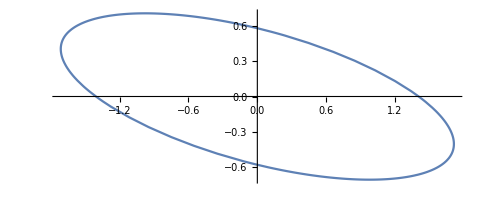

{(a (m^2+l^2 n) Cos[x]-b l m (-1+n) Sin[x])/(l^2+m^2),(-a l m (-1+n) Cos[x]+b (l^2+m^2 n) Sin[x])/(l^2+m^2)}

```mathematica
ParametricPlot[Rmat.r[x].{{1,0},{0,1},{0,0}},{x,0,2π}]
```

```mathematica
Vearth=FullSimplify[Rmat.v[x]]
```

{-(l L m (-1+n) (e+Cos[x])+L (m^2+l^2 n) Sin[x])/((l^2+m^2) ro μ),(L (l^2+m^2 n) (e+Cos[x])+l L m (-1+n) Sin[x])/((l^2+m^2) ro μ),-(L √(1-n^2) (m (e+Cos[x])+l Sin[x]))/(√(1+l^2/m^2) m ro μ)}

```mathematica
Angle=FullSimplify[Rearth.{1,0}/Norm[Rearth]]
```

(Abs[l^2+m^2] (a (m^2+l^2 n) Cos[x]-b l m (-1+n) Sin[x]))/((l^2+m^2) √(Abs[a (m^2+l^2 n) Cos[x]-b l m (-1+n) Sin[x]]^2+Abs[a l m (-1+n) Cos[x]-b (l^2+m^2 n) Sin[x]]^2))

1

```mathematica
l[π]
```

-1

Sin[x] (-Cos[γ] Sin[α]-Cos[α] Cos[β] Sin[γ])+2 Cos[x] (Cos[α] Cos[β] Cos[γ]-Sin[α] Sin[γ])

EulerMatrix::real: The angle measure 1.5708-0.102121 ⅈ should be real-valued.

EulerMatrix::ang: {1.29783,1.5708-0.102121 ⅈ,0} should be a list of three real-valued quantities.

EulerMatrix::real: The angle measure 1.5708-0.102121 ⅈ should be real-valued.

EulerMatrix::ang: {1.29783,1.5708-0.102121 ⅈ,0} should be a list of three real-valued quantities.

EulerMatrix::real: The angle measure 1.5708-0.102121 ⅈ should be real-valued.

General::stop: Further output of EulerMatrix::real will be suppressed during this calculation.

EulerMatrix::ang: {1.29783,1.5708-0.102121 ⅈ,0} should be a list of three real-valued quantities.

General::stop: Further output of EulerMatrix::ang will be suppressed during this calculation.

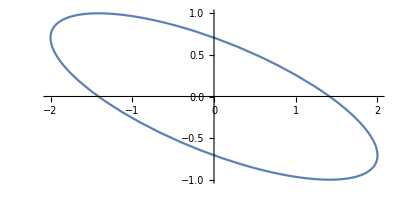

```mathematica
ParametricPlot[{2 Cos[x+π/4],Sin[x]},{x,0,2π
}]
```

```mathematica
Rmat=RotationMatrix[-ArcTan[l/m],{0,0,1}].EulerMatrix[{ArcTan[l/m],ArcCos[Sqrt[1-l^2-m^2]],0},{3,1,3}];
```

```mathematica
Rmat/.{l->0.3,m->0.4}
```

{{1.,0,0},{0,0.866025,-0.5},{0,0.5,0.866025}}

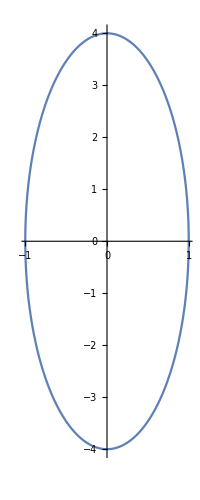

```mathematica
ParametricPlot[(Rmat/.{l->0.0,m->0.00001}).r[x].{{1,0},{0,1},{0,0}},{x,0,2π}]
```

```mathematica
Rmat.{1,0,0}
```

{Cos[a] Cos[b],Cos[b] Sin[a],-Sin[b]}

```mathematica
Rearth=FullSimplify[Rmat.r[x].{{1,0},{0,1},{0,0}}]
```

{a Cos[x],b √(1-l^2-m^2) Sin[x]}

```mathematica
Vearth=FullSimplify[Rmat.v[y]]
```

{-(L Sin[y])/(ro μ),(L √(1-l^2-m^2) (e+Cos[y]))/(ro μ),(L √(l^2+m^2) (e+Cos[y]))/(ro μ)}

```mathematica
Vearth.{{1,0},{0,1},{0,0}}
```

{-(L Sin[y])/(ro μ),(L √(1-l^2-m^2) (e+Cos[y]))/(ro μ)}

```mathematica
EulerMatrix[{40,135,65} π/180,{3,1,3}].{0,0,1}//N
```

{0.454519,-0.541675,-0.707107}